# 2.2

2.2a)

```mathematica
A={{σ +1,3},{-2,σ-1}};
Eigenvalues[A]
```

{-ⅈ √5+σ,ⅈ √5+σ}

```mathematica
ClearAll["Global`*"];
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];//Simplify

(*To be able to copy paste to Open TA*)
equationString=ToString[solution,InputForm];
equationModifiedString=ToLowerCase[StringReplace[equationString,{"["->"(","]"->")"}]]
Export["test.txt",{equationModifiedString}]
```

{{x(t) -> (e^(sigma*t)*(5*u*cos(sqrt(5)*t) + sqrt(5)*u*sin(sqrt(5)*t) + 3*sqrt(5)*v*sin(sqrt(5)*t)))/5, y(t) -> -1/5*(e^(sigma*t)*(-5*v*cos(sqrt(5)*t) + 2*sqrt(5)*u*sin(sqrt(5)*t) + sqrt(5)*v*sin(sqrt(5)*t)))}}

2.2c)

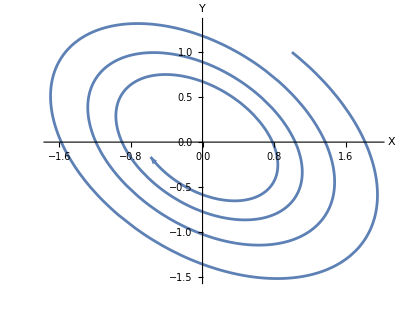

```mathematica
ClearAll["Global`*"];
sigma=-1/10;
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];

solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

streamPlot = StreamPlot[
  Evaluate[{eqns} /. {solX -> vx, solY -> u}],
  {X[t], -2, 2}, {Y[t], -2, 2}
];
trajPlot=ParametricPlot[{solX,solY}/. {u->1,v->1},{t,0,10},AxesLabel->{"X","Y"}];
trajPlot /. Line[x_] :> {Arrowheads[{.1}], Arrow[x]}
```

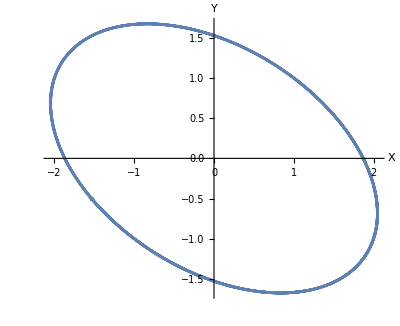

```mathematica
ClearAll["Global`*"];
sigma=0;
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];

solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

trajPlot=ParametricPlot[{solX,solY}/. {u->1,v->1},{t,0,10},AxesLabel->{"X","Y"}];
trajPlot /. Line[x_] :> {Arrowheads[{.1}], Arrow[x]}
```

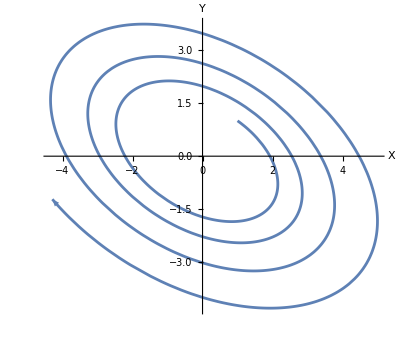

```mathematica
ClearAll["Global`*"];
sigma=1/10;
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];

solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

trajPlot=ParametricPlot[{solX,solY}/. {u->1,v->1},{t,0,10},AxesLabel->{"X","Y"}];
trajPlot /. Line[x_] :> {Arrowheads[{.1}], Arrow[x]}
```

2.2d)

```mathematica
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t]
```

{{X[t]→1/5 ⅇ^(-t/10) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t]),Y[t]→-1/5 ⅇ^(-t/10) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])}}

All cos and sin has the term sqrt(5) in front of the variable t. Therfore the period is stated by 2 pi/sqrt(5)

```mathematica
result=2 Pi/Sqrt[5]
```

(2 π)/(√5)

2.2 e)

```mathematica
ClearAll["Global`*"];
sigma=0;
solution =DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];
u=1;
v=1;
solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

(*Define the distance function from the origin*)
r[t_]:=Sqrt[(solX)^2+(solY)^2];

dr=D[r[t],t]
extremPoints=Solve[dr==0,t];
extremeR= r[t]/. extremPoints;

min1=Min[extremeR];
max1=Max[extremeR];
ratio=max1/min1 //Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::ztest: Unable to decide whether numeric quantities {(70+210 ⅈ)-14 √(-20+10 ⅈ) √(11-2 ⅈ),(10+30 ⅈ)-2 √(-20+10 ⅈ) √(11-2 ⅈ),(-5-15 ⅈ)+√(-20+10 ⅈ) √(11-2 ⅈ),(70-210 ⅈ)-14 √(-20-10 ⅈ) √(11+2 ⅈ),(10-30 ⅈ)-2 √(-20-10 ⅈ) √(11+2 ⅈ),(-5+15 ⅈ)+√(-20-10 ⅈ) √(11+2 ⅈ)} are equal to zero. Assuming they are.

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/25 (-5 Power[«2»]-4 Power[«2»])^2+1/25 (-5 Power[«2»]+3 Power[«2»])^2)-√(1/25 (Times[«2»]+Times[«2»])^2+1/25 (Times[«2»]+Times[«2»])^2).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/25 (5 Power[«2»]-4 Power[«2»])^2+1/25 (5 Power[«2»]+3 Power[«2»])^2)-√(1/25 (Times[«2»]+Times[«2»])^2+1/25 (Times[«2»]+Times[«2»])^2).

General::stop: Further output of Min::meprec will be suppressed during this calculation.

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(1/25 (Times[«2»]+Times[«2»])^2+1/25 (Times[«2»]+Times[«2»])^2)+√(1/25 (-5 Power[«2»]-3 Power[«2»])^2+1/25 (-5 Power[«2»]+4 Power[«2»])^2).

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(1/25 (Times[«2»]+Times[«2»])^2+1/25 (Times[«2»]+Times[«2»])^2)+√(1/25 (5 Power[«2»]-3 Power[«2»])^2+1/25 (5 Power[«2»]+4 Power[«2»])^2).

General::stop: Further output of Max::meprec will be suppressed during this calculation.

1/2 (1+√5)

2.2f)

```mathematica
ClearAll["Global`*"];
sigma=0;
solution=DSolve[{ X'[t]==(sigma+1)X[t]+3Y[t],Y'[t]== -2 X[t]+(sigma-1) Y[t],X[0]==u,Y[0]==v},{X[t],Y[t]},t];
u=1;
v=1;
solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

(*Define the distance function from the origin*)
r[t_]:=Sqrt[(solX)^2+(solY)^2];
dr=D[r[t],t];
ddr=D[dr[t],t];

extremPoints=Solve[dr==0,t];
extremPoints[[1]];//Simplify

t=t/. extremPoints[[1]]

solX=X[t]/. solution[[1]];
solY=Y[t]/. solution[[1]];

r[t_]:=Sqrt[(solX)^2+(solY)^2];

xValue=solX/.{u->1,v->1};
yValue=solY/. {u->1,v->1};
vector={xValue,yValue};

normVector=-Normalize[vector]// Simplify

(*To be able to copy paste to Open TA*)
equationString=ToString[normVector,InputForm];
equationModifiedString=ToLowerCase[StringReplace[equationString,{"["->"(","]"->")"}]];
Export["test.txt",{equationModifiedString}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-ArcCos[-√(1/14 (7-3 √5))]/(√5)

{(5 √(7-3 √5)+4 √(5 (7+3 √5)))/(7 √(5 (5+√5))),(5 √(7-3 √5)-3 √(5 (7+3 √5)))/(7 √(5 (5+√5)))}